1.4

50

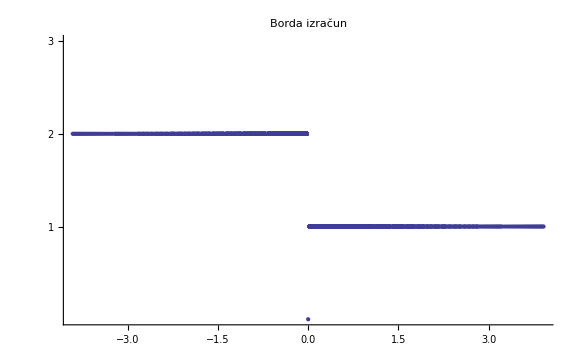

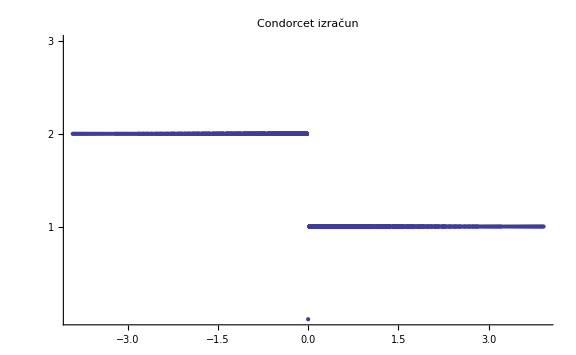

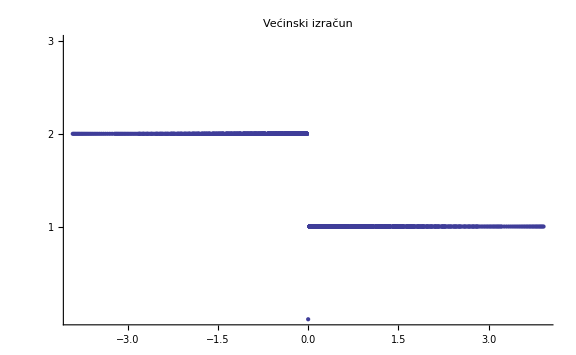

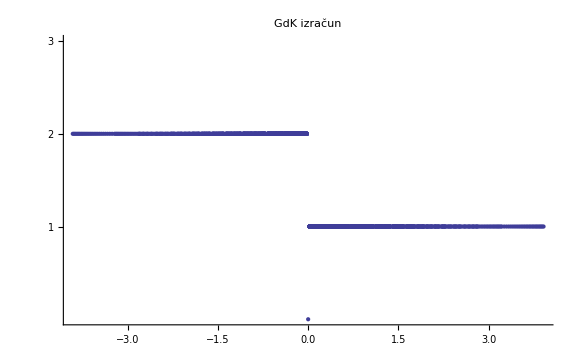

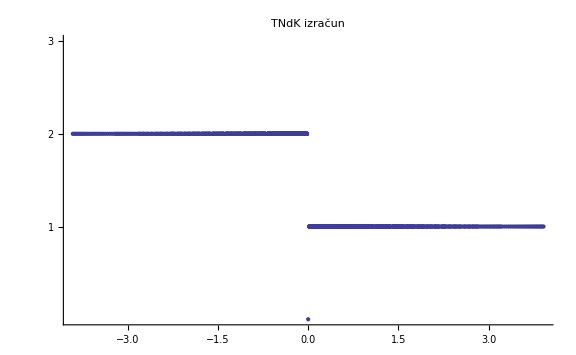

```mathematica
d=1.4
n=50
Borda=Table[0,{i,n},{j,n}];
Condorcet=Table[0,{i,n},{j,n}];
Vecinski=Table[0,{i,n},{j,n}];
GdK=Table[0,{i,n},{j,n}];
TNdK=Table[0,{i,n},{j,n}];

For[i=1,i<n+1,i++,
For[j=1,j<n+1,j++,
alfa={i,0,0,0,j,0};

(*Borda*)
BoA=2*(alfa[[1]]+alfa[[4]])+alfa[[2]]+alfa[[5]];
BoB=2*(alfa[[3]]+alfa[[5]])+alfa[[1]]+alfa[[6]];
BoC=2*(alfa[[2]]+alfa[[6]])+alfa[[3]]+alfa[[4]];
Which[And[BoA>BoB,BoA>BoC],Borda[[i,j]]=1,And[BoB>BoA,BoB>BoC],Borda[[i,j]]=2,And[BoC>BoA,BoC>BoB],Borda[[i,j]]=3,True,Borda[[i,j]]=0];

(*Condorcet*)
ConAB=alfa[[1]]+alfa[[2]]+alfa[[4]]-(alfa[[3]]+alfa[[5]]+alfa[[6]]);
ConAC=alfa[[1]]+alfa[[4]]+alfa[[5]]-(alfa[[2]]+alfa[[3]]+alfa[[6]]);
ConBC=alfa[[1]]+alfa[[3]]+alfa[[5]]-(alfa[[2]]+alfa[[4]]+alfa[[6]]);
Which[And[ConAB>0,ConAC>0],Condorcet[[i,j]]=1,And[ConAB<0,ConBC>0],Condorcet[[i,j]]=2,And[ConAC<0,ConBC<0],Condorcet[[i,j]]=3,True,Condorcet[[i,j]]=0];

(*Vecinski*)
VeA=alfa[[1]]+alfa[[4]];
VeB=alfa[[3]]+alfa[[5]];
VeC=alfa[[2]]+alfa[[6]];
Which[And[VeA>VeB,VeA>VeC],Vecinski[[i,j]]=1,And[VeB>VeA,VeB>VeC],Vecinski[[i,j]]=2,And[VeC>VeA,VeC>VeB],Vecinski[[i,j]]=3,True,Vecinski[[i,j]]=0];


(*GdK*)
GdKA=alfa[[2]]+alfa[[5]]+(alfa[[3]]+alfa[[6]])*2^d;
GdKB=alfa[[1]]+alfa[[6]]+(alfa[[2]]+alfa[[4]])*2^d;
GdKC=alfa[[3]]+alfa[[4]]+(alfa[[1]]+alfa[[5]])*2^d;
Which[And[GdKA<GdKB,GdKA<GdKC],GdK[[i,j]]=1,And[GdKB<GdKA,GdKB<GdKC],GdK[[i,j]]=2,And[GdKC<GdKA,GdKC<GdKB],GdK[[i,j]]=3,True,GdK[[i,j]]=0];

(*TNdK*)
MdK={{alfa[[2]]+alfa[[5]]+(alfa[[3]]+alfa[[6]])*2^d,alfa[[1]]+alfa[[3]]+alfa[[4]]+alfa[[6]],alfa[[2]]+alfa[[5]]+(alfa[[1]]+alfa[[4]])*2^d},{alfa[[1]]+alfa[[6]]+(alfa[[2]]+alfa[[4]])*2^d,alfa[[2]]+alfa[[3]]+alfa[[4]]+alfa[[5]],alfa[[1]]+alfa[[6]]+(alfa[[3]]+alfa[[5]])*2^d},{alfa[[3]]+alfa[[4]]+(alfa[[1]]+alfa[[5]])*2^d,alfa[[1]]+alfa[[2]]+alfa[[5]]+alfa[[6]],alfa[[3]]+alfa[[4]]+(alfa[[2]]+alfa[[6]])*2^d}}; 
TNdKABC=MdK[[1,1]]+MdK[[2,2]]+MdK[[3,3]];
TNdKACB=MdK[[1,1]]+MdK[[2,3]]+MdK[[3,2]];
TNdKBAC=MdK[[1,2]]+MdK[[2,1]]+MdK[[3,3]];
TNdKBCA=MdK[[1,3]]+MdK[[2,1]]+MdK[[3,2]];
TNdKCAB=MdK[[1,2]]+MdK[[2,3]]+MdK[[3,1]];
TNdKCBA=MdK[[1,3]]+MdK[[2,2]]+MdK[[3,1]];
Which[And[TNdKABC<TNdKACB,TNdKABC<TNdKBAC,TNdKABC<TNdKBCA,TNdKABC<TNdKCAB,TNdKABC<TNdKCBA],TNdK[[i,j]]=1,And[TNdKACB<TNdKABC,TNdKACB<TNdKBAC,TNdKACB<TNdKBCA,TNdKACB<TNdKCAB,TNdKACB<TNdKCBA],TNdK[[i,j]]=1,And[TNdKBAC<TNdKABC,TNdKBAC<TNdKACB,TNdKBAC<TNdKBCA,TNdKBAC<TNdKCAB,TNdKBAC<TNdKCBA],TNdK[[i,j]]=2,And[TNdKBCA<TNdKABC,TNdKBCA<TNdKACB,TNdKBCA<TNdKBAC,TNdKBCA<TNdKCAB,TNdKBCA<TNdKCBA],TNdK[[i,j]]=2,And[TNdKCAB<TNdKABC,TNdKCAB<TNdKACB,TNdKCAB<TNdKBAC,TNdKCAB<TNdKBCA,TNdKCAB<TNdKCBA],TNdK[[i,j]]=3,And[TNdKCBA<TNdKABC,TNdKCBA<TNdKACB,TNdKCBA<TNdKBAC,TNdKCBA<TNdKBCA,TNdKCBA<TNdKCAB],TNdK[[i,j]]=3,True,TNdK[[i,j]]=0];

]]

MatrixForm[Borda];
MatrixForm[Condorcet];
MatrixForm[Vecinski];
MatrixForm[GdK];
MatrixForm[TNdK];

(*CRTANJE BORDA*)
BordaRez=Table[{0,0},{i,n^2}];
For[i=1,i<n+1,i++,
For[j=1,j<n+1,j++,
BordaRez[[(i-1)*n+j,1]]=Log[i/j];
BordaRez[[(i-1)*n+j,2]]=Borda[[i,j]]
]]
BordaRez=DeleteDuplicates[BordaRez];
ListPlot[BordaRez,PlotRange->{0,3},Ticks->{Automatic,{1,2,3}},PlotLabel->"Borda izračun",ImageSize->Large]

(*CRTANJE Condorcet*)
CondorcetRez=Table[{0,0},{i,n^2}];
For[i=1,i<n+1,i++,
For[j=1,j<n+1,j++,
CondorcetRez[[(i-1)*n+j,1]]=Log[i/j];
CondorcetRez[[(i-1)*n+j,2]]=Condorcet[[i,j]]
]]
CondorcetRez=DeleteDuplicates[CondorcetRez];
ListPlot[CondorcetRez,PlotRange->{0,3},Ticks->{Automatic,{1,2,3}},PlotLabel->"Condorcet izračun",ImageSize->Large]

(*CRTANJE Vecinski*)
VecinskiRez=Table[{0,0},{i,n^2}];
For[i=1,i<n+1,i++,
For[j=1,j<n+1,j++,
VecinskiRez[[(i-1)*n+j,1]]=Log[i/j];
VecinskiRez[[(i-1)*n+j,2]]=Vecinski[[i,j]]
]]
VecinskiRez=DeleteDuplicates[VecinskiRez];
ListPlot[VecinskiRez,PlotRange->{0,3},Ticks->{Automatic,{1,2,3}},PlotLabel->"Većinski izračun",ImageSize->Large]

(*CRTANJE GdK*)
GdKRez=Table[{0,0},{i,n^2}];
For[i=1,i<n+1,i++,
For[j=1,j<n+1,j++,
GdKRez[[(i-1)*n+j,1]]=Log[i/j];
GdKRez[[(i-1)*n+j,2]]=GdK[[i,j]]
]]
GdKRez=DeleteDuplicates[GdKRez];
ListPlot[GdKRez,PlotRange->{0,3},Ticks->{Automatic,{1,2,3}},PlotLabel->"GdK izračun",ImageSize->Large]

(*CRTANJE TNdK*)
TNdKRez=Table[{0,0},{i,n^2}];
For[i=1,i<n+1,i++,
For[j=1,j<n+1,j++,
TNdKRez[[(i-1)*n+j,1]]=Log[i/j];
TNdKRez[[(i-1)*n+j,2]]=TNdK[[i,j]]
]]
TNdKRez=DeleteDuplicates[TNdKRez];
ListPlot[TNdKRez,PlotRange->{0,3},Ticks->{Automatic,{1,2,3}},PlotLabel->"TNdK izračun",ImageSize->Large]
```